# Moire Lattice wavelength

```mathematica
ClearAll["Global`*"]
```

```mathematica
gn=6;
bn=1;
```

```mathematica
g=Table[(2*π/(a))*{Sin[i*π/(gn/2)],Cos[i*π/(gn/2)]},{i,0,gn-1}];
b=Table[(2*π/(a*(1+ϵ)))*{Sin[(i*π/(bn/2)+Re[θ])],Cos[(i*π/(bn/2)+Re[θ])]},{i,0,bn-1}];
k=Table[g[[i]]-b[[j]],{i,1,gn},{j,1,bn}];


Norm[k[[1]][[1]]];





λ[a_,ϵ_,θ_]=Table[(2*π)/Norm[k[[i]][[j]]]//Flatten,{i,1,gn},{j,1,bn}];
```

```mathematica
FT[a_,ϵ_,θ_]=Table[λ[a,ϵ,θ][[i]][[j]],{i,1,gn},{j,1,bn}];
```

```mathematica
eps=0;
a=2.044094*10^-(05);
```

```mathematica
filtered=Select[FT[1,0,x],(.1<#[[2]]<.5)&]
```

Part::partw: Part 2 of {(2 π)/(√(Abs[Times[«2»]+Times[«3»]]^2+4 π^2 Abs[Sin[«1»]]^2))} does not exist.

Part::partw: Part 2 of {(2 π)/(√(Abs[π+Times[«3»]]^2+Abs[Times[«2»]+Times[«3»]]^2))} does not exist.

Part::partw: Part 2 of {(2 π)/(√(Abs[Times[«2»]+Times[«3»]]^2+Abs[Times[«2»]+Times[«3»]]^2))} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{}

```mathematica
2*π/Sqrt[3]/FT[a,2,0*π/180]//N//ScientificForm
```

{{1.18312×10^5},{1.56511×10^5},{2.13289×10^5},{2.36623×10^5},{2.13289×10^5},{1.56511×10^5}}

```mathematica
pp1=Plot3D[1/FT[1,y,x],{x,0,2π},{y,-1,1},RegionFunction->Function[{x,y,z},Sqrt[2+Sqrt[3]]<z],PlotStyle->{Blue}];
pp2=Plot3D[1/FT[1,y,x],{x,0,2π},{y,-1,1},RegionFunction->Function[{x,y,z},Sqrt[2+Sqrt[3]]>z > 1.73],PlotStyle->{Orange}];
pp3=Plot3D[1/FT[1,y,x],{x,0,2π},{y,-1,1},RegionFunction->Function[{x,y,z},1.73>z > Sqrt[2]],PlotStyle->{Green}];
pp4=Plot3D[1/FT[1,y,x],{x,0,2π},{y,-1,1},RegionFunction->Function[{x,y,z},Sqrt[2]>z >= 1],PlotStyle->{Red}];
pp5=Plot3D[1/FT[1,y,x],{x,0,2π},{y,-1,1},RegionFunction->Function[{x,y,z},1>z ≥1/Sqrt[2+Sqrt[3]]],PlotStyle->{Gray}];
pp6=Plot3D[1/FT[1,y,x],{x,0,2π},{y,-1,1},RegionFunction->Function[{x,y,z},1/Sqrt[2+Sqrt[3]]>z > 0],PlotStyle->{Black}];
```

```mathematica
Show[pp1,pp2,pp3,pp4,pp5,pp6,PlotRange->{0,2}]
```

-Graphics3D-

```mathematica
ToExpression["\\sin a",TeXForm,HoldForm]
```

sin a

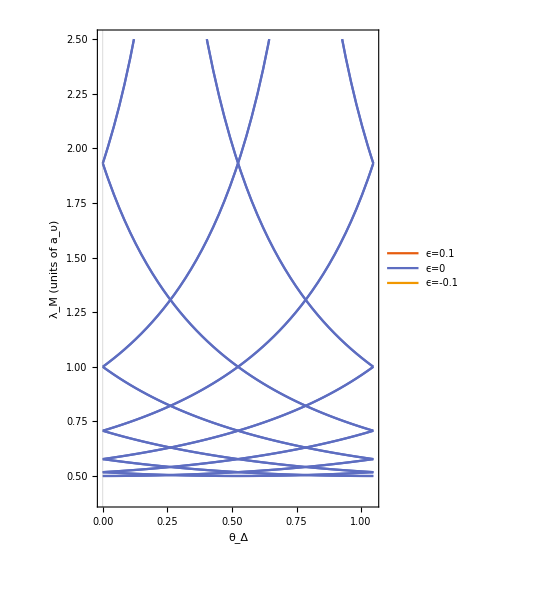

```mathematica
P1=Plot[{0*FT[1,0.1,x],FT[1,0,x],0*FT[1,-0.1,x]},{x,0,π/3},FrameLabel->{Subscript["θ","Δ" ],ToString[Subscript["λ","M"] ,FormatType->StandardForm]<> " (units of " <> ToString[Subscript["a","υ"] ,FormatType->StandardForm]<> ")"},PlotTheme->"Scientific",AspectRatio->1.5,LabelStyle->Directive[22,FontFamily->"Latin Modern Roman Unslanted"],PlotLegends->{"ϵ=0.1","ϵ=0","ϵ=-0.1"},PlotRange->{{0,π/3},{0.4,2.5}},TicksStyle->Directive[Blue, Thick, Italic],FrameTicksStyle->Directive[22,FontFamily->"Latin Modern Roman"]]
```

```mathematica
Export["~/Desktop/Moire_higherk_epsrange1.pdf",P1,"AllowRasterization"->False]
```

~/Desktop/Moire_higherk_epsrange1.pdf

```mathematica
FT[a,-0.5,0]//N//ScientificForm



a=1;
```

{{1.×10^1},{5.7735},{3.77964},{3.33333},{3.77964},{5.7735}}

```mathematica
p1k=Plot[1/FT[a,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Black},RegionFunction->Function[{x,y},Sqrt[2+Sqrt[3]]<y],PlotLegends->{"1",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24},Ticks->{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π}, {0,1,2}}];
p2k=Plot[1/FT[a,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Gray},RegionFunction->Function[{x,y},Sqrt[2+Sqrt[3]]>y > 1.73],PlotLegends->{"2",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24},Ticks->{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π}, {0,1,2}}];
p3k=Plot[1/FT[a,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Red},RegionFunction->Function[{x,y},1.73>y > Sqrt[2]],PlotLegends->{"3",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24},Ticks->{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π}, {0,1,2}}];p4k=Plot[1/FT[a,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Green},RegionFunction->Function[{x,y},Sqrt[2]>y >= 1],PlotLegends->{"4",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24},Ticks->{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π}, {0,1,2}}];
p5k=Plot[1/FT[a,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Orange},RegionFunction->Function[{x,y},1>y ≥1/Sqrt[2+Sqrt[3]]],PlotLegends->{"5",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24},Ticks->{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π}, {0,1,2}}];
p6k=Plot[1/FT[a,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Blue},RegionFunction->Function[{x,y},1/Sqrt[2+Sqrt[3]]>y > 0],PlotLegends->{"6",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24},Ticks->{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π}, {0,1,2}}];
```

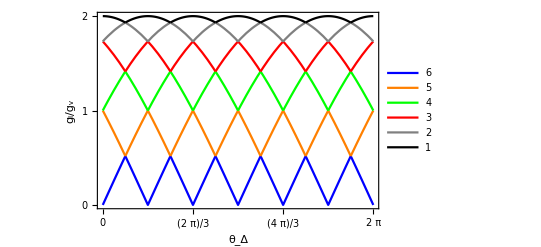

```mathematica
Show[p6k,p5k,p4k,p3k,p2k,p1k,PlotRange->{{0,2π},{0,2}},Frame->True,FrameTicks->{{{0,1,2},None},{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π},None}},FrameLabel->{Subscript["θ","Δ" ],ToString[Style[Subscript["g","l"],Italic] ,FormatType->StandardForm]<> "/" <> ToString[Style[Subscript["g","v"] ,Italic],FormatType->StandardForm]}]
```

```mathematica
p1r=Plot[FT[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Blue},RegionFunction->Function[{x,y},1.932<y],PlotLegends->{"1"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p2r=Plot[FT[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Orange},RegionFunction->Function[{x,y},1.932>y >= 1.0],PlotLegends->{"2"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p3r=Plot[FT[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Green},RegionFunction->Function[{x,y},1.0>y >= 1/Sqrt[2]],PlotLegends->{"3"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];p4r=Plot[FT[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Red},RegionFunction->Function[{x,y},1/Sqrt[2]>y >= 1/Sqrt[3]],PlotLegends->{"4"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p5r=Plot[FT[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Gray},RegionFunction->Function[{x,y},1/Sqrt[3]>y >= 0.5176],PlotLegends->{"5"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p6r=Plot[FT[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Black},RegionFunction->Function[{x,y},0.5176>y > 0],PlotLegends->{"6"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
```

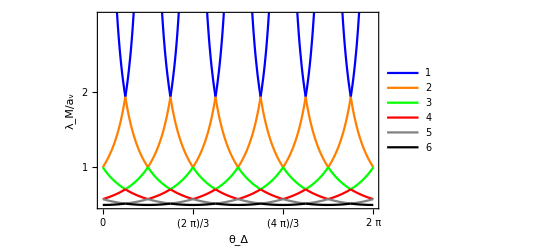

```mathematica
Show[p1r,p2r,p3r,p4r,p5r,p6r,PlotRange->{{0,2π},{0.5,3}},Frame->True,FrameTicks->{{{0,1,2},None},{{0, π/3,2*π/3,π,4*π/3, 5*π/3,2π},None}},FrameLabel->{Subscript["θ","Δ" ],ToString[Style[Subscript["λ","M"],Italic] ,FormatType->StandardForm]<> "/" <> ToString[Style[Subscript["a","v"] ,Italic],FormatType->StandardForm]}]
```

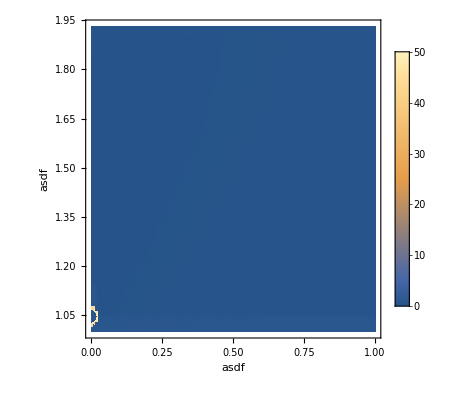

```mathematica
DensityPlot[FT[1,e,x],{e,0,1},{x,0,2π},ColorFunctionScaling->True,PlotLegends->Automatic,PlotPoints->100,PlotRange->{Automatic,Automatic,{0,50}},Axes->True,AxesOrigin->{0,0},AxesLabel->{"asdf","asdf"},RegionFunction->Function[{x,y},1.932>y > 1.0]]
```

```mathematica
Max[FT[2.044094*10^(-5),0,11*π/180]]//ScientificForm
```

1.06635×10^-4

```mathematica
FT[a,0,o]//Simplify
```

{{1/(√(Abs[(-1+Cos[Re[o]])/a]^2+Abs[Sin[Re[o]]/a]^2))},{(2 π)/(√(Abs[(π-2 π Cos[Re[o]])/a]^2+π^2 Abs[(√3-2 Sin[Re[o]])/a]^2))},{(2 π)/(√(Abs[(π+2 π Cos[Re[o]])/a]^2+π^2 Abs[(√3-2 Sin[Re[o]])/a]^2))},{1/(√(Abs[Sin[Re[o]]/a]^2+(1+Cos[Re[o]])^2/Abs[a]^2))},{(2 π)/(√(Abs[(π+2 π Cos[Re[o]])/a]^2+π^2 Abs[(√3+2 Sin[Re[o]])/a]^2))},{(2 π)/(√(Abs[(π-2 π Cos[Re[o]])/a]^2+π^2 Abs[(√3+2 Sin[Re[o]])/a]^2))}}

```mathematica
(1-Cos[Re[o]]+Re[e])^2+Sin[Re[o]]^2//Simplify
```

(1-Cos[Re[o]]+Re[e])^2+Sin[Re[o]]^2

```mathematica
TrigExpand[(Cos[x+π/6])^2]
```

1/2+Cos[x]^2/4-1/2 √3 Cos[x] Sin[x]-Sin[x]^2/4

```mathematica
(1-Cos[Re[o]])^2//TrigExpand
```

1-2 Cos[Re[o]]+Cos[Re[o]]^2

```mathematica
Max[FT[2.044094*10^{-5},0,11π/180]]//ScientificForm
```

FT[{2.04409×10^-5},0,(11 π)/180]

```mathematica
"1.06635"×10^("-4")
```

0.000106635

```mathematica
Abs[((1.06635×10^-4-1.0954×10^-4)/(1.0954×10^-4))*100]
```

2.652

```mathematica
S[e_,θ_]=(1+e)/Sqrt[(e^2 + 2*(1-Cos[θ])*(1+e))]
```

(1+e)/(√(e^2+2 (1+e) (1-Cos[θ])))

```mathematica
Denominator[(1+e)/(√(e^2+2 (1+e) (1-Cos[θ])))]
```

√(e^2+2 (1+e) (1-Cos[θ]))

```mathematica
D[√(e^2+2 (1+e) (1-Cos[θ])), θ]
```

((1+e) Sin[θ])/(√(e^2+2 (1+e) (1-Cos[θ])))

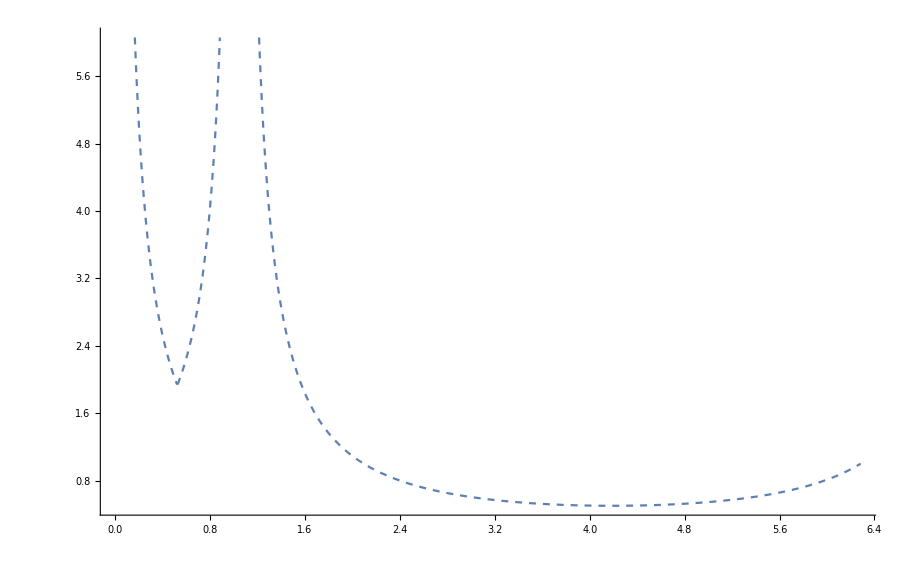

```mathematica
Plot[{S[0,Min[{θ,π/3-θ}]],Max[FT[1,0,θ]]},{θ,0,2*π},PlotStyle->{Dashed,Dotted}]
```

```mathematica
FT[a,e,θ]
```

{{(2 π)/(√(Abs[(2 π)/a-(2 π Cos[Re[θ]])/(a (1+e))]^2+4 π^2 Abs[Sin[Re[θ]]/(a (1+e))]^2))},{(2 π)/(√(Abs[π/a-(2 π Cos[Re[θ]])/(a (1+e))]^2+Abs[(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+e))]^2))},{(2 π)/(√(Abs[-π/a-(2 π Cos[Re[θ]])/(a (1+e))]^2+Abs[(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+e))]^2))},{(2 π)/(√(Abs[-(2 π)/a-(2 π Cos[Re[θ]])/(a (1+e))]^2+4 π^2 Abs[Sin[Re[θ]]/(a (1+e))]^2))},{(2 π)/(√(Abs[-π/a-(2 π Cos[Re[θ]])/(a (1+e))]^2+Abs[-(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+e))]^2))},{(2 π)/(√(Abs[π/a-(2 π Cos[Re[θ]])/(a (1+e))]^2+Abs[-(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+e))]^2))}}

```mathematica
FT[a,0,o]
```

{{(2 π)/(√(Abs[(2 π)/a-(2 π Cos[Re[o]])/a]^2+4 π^2 Abs[Sin[Re[o]]/a]^2))},{(2 π)/(√(Abs[π/a-(2 π Cos[Re[o]])/a]^2+Abs[(√3 π)/a-(2 π Sin[Re[o]])/a]^2))},{(2 π)/(√(Abs[-π/a-(2 π Cos[Re[o]])/a]^2+Abs[(√3 π)/a-(2 π Sin[Re[o]])/a]^2))},{(2 π)/(√(Abs[-(2 π)/a-(2 π Cos[Re[o]])/a]^2+4 π^2 Abs[Sin[Re[o]]/a]^2))},{(2 π)/(√(Abs[-π/a-(2 π Cos[Re[o]])/a]^2+Abs[-(√3 π)/a-(2 π Sin[Re[o]])/a]^2))},{(2 π)/(√(Abs[π/a-(2 π Cos[Re[o]])/a]^2+Abs[-(√3 π)/a-(2 π Sin[Re[o]])/a]^2))}}

```mathematica
FullSimplify[FT[a,e,o],Assumptions->{a ≥0, a∈ Reals,e≥0, e∈ Reals,o≥0, o≤2π,o∈ Reals}]
```

{{(a (1+e))/(√(2+e (2+e)-2 (1+e) Cos[o]))},{(a (1+e))/(√(2+e (2+e)-(1+e) Cos[o]-√3 (1+e) Sin[o]))},{(a (1+e))/(√(2+e (2+e)+(1+e) Cos[o]-√3 (1+e) Sin[o]))},{(a (1+e))/(√(2+e (2+e)+2 (1+e) Cos[o]))},{(a (1+e))/(√(2+e (2+e)+(1+e) Cos[o]+√3 (1+e) Sin[o]))},{(a (1+e))/(√(2+e (2+e)-(1+e) Cos[o]+√3 (1+e) Sin[o]))}}

```mathematica
FG[a_,e_,o_]={{(a (1+e))/(√(2+e (2+e)-(1+e) Cos[o]-√3 (1+e) Sin[o]))},{(a (1+e))/(√(2+e (2+e)+(1+e) Cos[o]-√3 (1+e) Sin[o]))},{(a (1+e))/(√((1+e+Cos[o])^2+Sin[o]^2))},{(a (1+e))/(√(2+e (2+e)+(1+e) Cos[o]+√3 (1+e) Sin[o]))},{(a (1+e))/(√(2+e (2+e)-(1+e) Cos[o]+√3 (1+e) Sin[o]))},{(a (1+e))/(√((1+e-Cos[o])^2+Sin[o]^2))}};
```

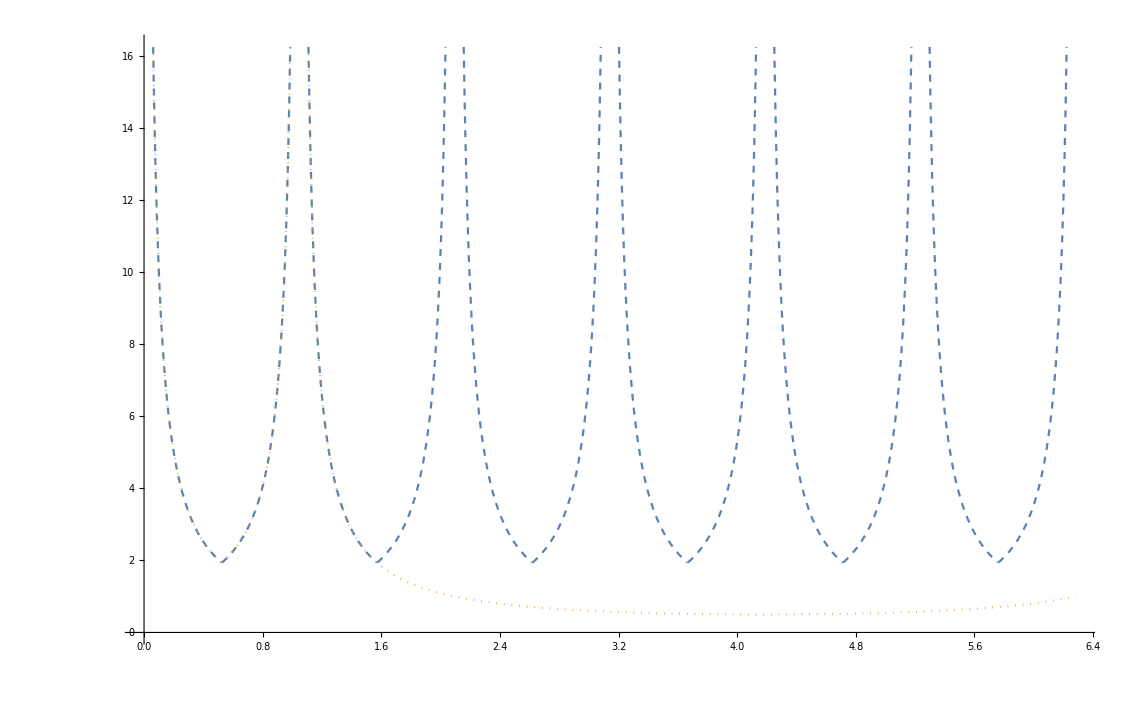

```mathematica
Plot[{Max[FG[1,0,x]],S[0,Min[{x,π/3-x}]]},{x,0,2*π},PlotStyle->{Dashed,Dotted}]
```

```mathematica
TB=Table[{F[θ],θ},{θ,0.01,2π,0.01}];
```

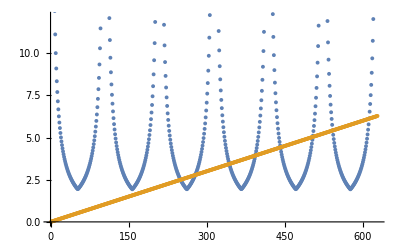

/Users/mlxd/Desktop/Lambda_m.csv

```mathematica
ListPlot[Transpose[TB]]
Export["/Users/mlxd/Desktop/Lambda_m.csv",TB,"CSV"]
```

```mathematica
FT[a,d,c]//FullSimplify
```

$Aborted

```mathematica
λ
```

{{(2 π)/(√(Abs[(2 π)/a-(2 π Cos[Re[θ]])/(a (1+Re[ϵ]))]^2+4 π^2 Abs[Sin[Re[θ]]/(a (1+Re[ϵ]))]^2))},{(2 π)/(√(Abs[π/a-(2 π Cos[Re[θ]])/(a (1+Re[ϵ]))]^2+Abs[(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+Re[ϵ]))]^2))},{(2 π)/(√(Abs[-π/a-(2 π Cos[Re[θ]])/(a (1+Re[ϵ]))]^2+Abs[(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+Re[ϵ]))]^2))},{(2 π)/(√(Abs[-(2 π)/a-(2 π Cos[Re[θ]])/(a (1+Re[ϵ]))]^2+4 π^2 Abs[Sin[Re[θ]]/(a (1+Re[ϵ]))]^2))},{(2 π)/(√(Abs[-π/a-(2 π Cos[Re[θ]])/(a (1+Re[ϵ]))]^2+Abs[-(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+Re[ϵ]))]^2))},{(2 π)/(√(Abs[π/a-(2 π Cos[Re[θ]])/(a (1+Re[ϵ]))]^2+Abs[-(√3 π)/a-(2 π Sin[Re[θ]])/(a (1+Re[ϵ]))]^2))}}

```mathematica
F[π/6]//N
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -√2\ π/-π + √3\ π + 2\ π/√π^2 + (2\ π - Power[« 2 »]\ π)^2.

1.93185

```mathematica
Max[FT[2.04409*10^(-5),0,11π/180]]//N//ScientificForm
```

1.06634×10^-4

```mathematica
Mod[{1,2,3,4,5,6},6]+1
```

{2,3,4,5,6,1}

```mathematica
Mod[{1,2,3,4,5,6},6]+1
```

{2,3,4,5,6,1}

```mathematica
π/2//N
```

1.5708

```mathematica
T1=Table[2*π/FT[1,eps,x],{x,0.00000001,2π-0.000000001,0.01}]
```

{{{6.28319×10^-8},{6.28319},{10.8828},{12.5664},{10.8828},{6.28319}},{{0.0628317},{6.22869},{10.8512},{12.5662},{10.9141},{6.33752}},626,{{0.0200138},{6.30051},{10.8928},{12.5664},{10.8728},{6.26584}}}
 |  |  |  |

```mathematica
Export["/Users/mlxd/Desktop/HigherK.csv",T1]
```

/Users/mlxd/Desktop/HigherK.csv

```mathematica
T1a=T1//Grid;
```

```mathematica
Select[T1,# [[1]][[1]]<1&];
```

```mathematica
T1a[[1]][[1]][[1]][[1]]
```

1.×10^-8

```mathematica
T1b=T1a//.{x_list} :> x;
```

{{{1.×10^-8},{1.},{1.73205},{2.},{1.73205},{1.}},{{0.00999997},{0.991327},{1.72703},{1.99998},{1.73703},{1.00865}},625,{{0.0131852},{1.0114},{1.73861},{1.99996},{1.72542},{0.98856}},{{0.0031853},{1.00276},{1.73364},{2.},{1.73046},{0.99724}}}
 |  |  |  |

```mathematica
1/FT[1,ϵ,x]
```

{{(√(Abs[2 π-(2 π Cos[Re[x]])/(1+ϵ)]^2+4 π^2 Abs[Sin[Re[x]]/(1+ϵ)]^2))/(2 π)},{(√(Abs[π-(2 π Cos[Re[x]])/(1+ϵ)]^2+Abs[√3 π-(2 π Sin[Re[x]])/(1+ϵ)]^2))/(2 π)},{(√(Abs[-π-(2 π Cos[Re[x]])/(1+ϵ)]^2+Abs[√3 π-(2 π Sin[Re[x]])/(1+ϵ)]^2))/(2 π)},{(√(Abs[-2 π-(2 π Cos[Re[x]])/(1+ϵ)]^2+4 π^2 Abs[Sin[Re[x]]/(1+ϵ)]^2))/(2 π)},{(√(Abs[-π-(2 π Cos[Re[x]])/(1+ϵ)]^2+Abs[-√3 π-(2 π Sin[Re[x]])/(1+ϵ)]^2))/(2 π)},{(√(Abs[π-(2 π Cos[Re[x]])/(1+ϵ)]^2+Abs[-√3 π-(2 π Sin[Re[x]])/(1+ϵ)]^2))/(2 π)}}

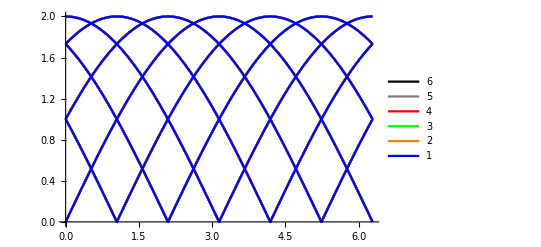

```mathematica
p1=Plot[kk[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Blue},PlotLegends->{"1",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p2=Plot[kk[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Orange},PlotLegends->{"2",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p3=Plot[kk[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Green},PlotLegends->{"3",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];p4=Plot[kk[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Red},PlotLegends->{"4",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p5=Plot[kk[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Gray},PlotLegends->{"5",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p6=Plot[kk[1,eps,x],{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Black},PlotLegends->{"6",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];

Show[p6,p5,p4,p3,p2,p1,PlotRange->{0,2}]
```

```mathematica
kk[a_,ϵ_,θ_]=Table[Norm[k[[i]][[j]]]/(2*π),{i,1,gn},{j,1,bn}];
```

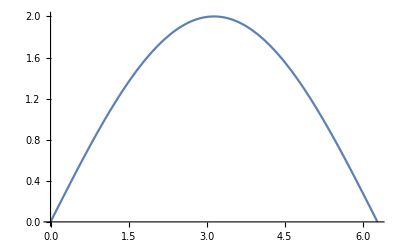

```mathematica
Plot[(2*Sin[x/2]),{x,0,2π}]
```

```mathematica
Plot[Sqrt[2*(1-Cos[x])],{x,0,2π}]
```

-Graphics-

```mathematica
{4*π/Sqrt[3]}.{1/{FT[1,0,π/12].{2.0441*10^{-5}}}}//N//ScientificForm
```

{{{9.26563×10^4},{2.71654×10^5},{5.63175×10^5},{7.03794×10^5},{6.55832×10^5},{4.3214×10^5}}}

```mathematica
Sqrt[2+Sqrt[3]]//N
```

1.93185

```mathematica
TT=Table[(4*π/Sqrt[3])*(1/(FT[1,0,ii*π/180]*(2.0441*10^(-5))))//N//ScientificForm,{ii,0,60,0.5}];
```

FlattenAt[{{0.},{3.54934×10^5},{6.14763×10^5},{7.09867×10^5},{6.14763×10^5},{3.54934×10^5}}]

```mathematica
TTT=Table[TT[[ii]][[1]][[jj]][[1]],{ii,1,60*2},{jj,1,6}];
```

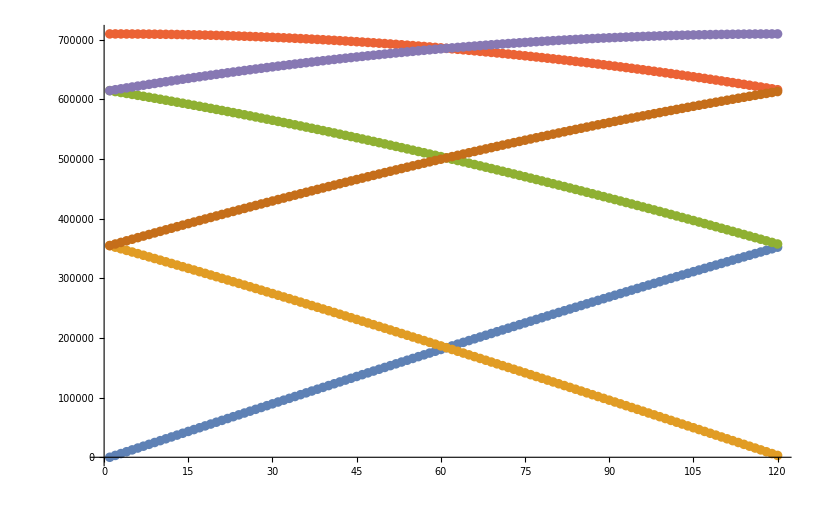

```mathematica
ListPlot[TTT//Transpose]
```

```mathematica
22.5π/180//N
```

0.392699

```mathematica
180/24
```

15/2

```mathematica
180/7.5
```

24.

```mathematica
π/8//N
```

0.392699

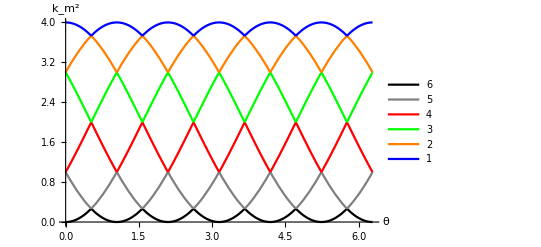

```mathematica
p1=Plot[(1/FT[1,eps,x])^2,{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Blue},RegionFunction->Function[{x,y},2+Sqrt[3]<y],PlotLegends->{"1",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p2=Plot[(1/FT[1,eps,x])^2,{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Orange},RegionFunction->Function[{x,y},2+Sqrt[3]>y >3],PlotLegends->{"2",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p3=Plot[(1/FT[1,eps,x])^2,{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Green},RegionFunction->Function[{x,y},3>y > 2],PlotLegends->{"3",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];p4=Plot[(1/FT[1,eps,x])^2,{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Red},RegionFunction->Function[{x,y},2>y >= 1],PlotLegends->{"4",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p5=Plot[(1/FT[1,eps,x])^2,{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Gray},RegionFunction->Function[{x,y},1>y ≥1/(2+Sqrt[3])],PlotLegends->{"5",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];
p6=Plot[(1/FT[1,eps,x])^2,{x,0,2π},PlotPoints->50, PlotStyle->{Thick,Black},RegionFunction->Function[{x,y},1/(2+Sqrt[3])>y > 0],PlotLegends->{"6",FontSize->24},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->24}];

Show[p6,p5,p4,p3,p2,p1,PlotRange->{0,4},AxesLabel->{θ,(k_m)^2}]
```

```mathematica
(1/(2+Sqrt[3]))^(1/2)//N
```

0.517638

```mathematica
T2=Table[(1/(FT[1,0,ii])^2)//N//ScientificForm,{ii,0,2π,0.001}]
```

{{{0.},{1.},{3.},{4.},{3.},{1.}},{{1.×10^-6},{9.98268×10^-1},{2.99827},{4.},{3.00173},{1.00173}},{{4.×10^-6},{9.96538×10^-1},{2.99653},{4.},{3.00346},{1.00347}},6278,{{4.77557×10^-6},{1.00379},{3.00378},{4.},{2.99621},{9.96217×10^-1}},{{1.40495×10^-6},{1.00205},{3.00205},{4.},{2.99795},{9.97948×10^-1}},{{3.43388×10^-8},{1.00032},{3.00032},{4.},{2.99968},{9.99679×10^-1}}}
 |  |  |  |

```mathematica
Export["/Users/mlxd/Desktop/HigherK2_6k.csv",T2]
```

/Users/mlxd/Desktop/HigherK2_6k.csv

```mathematica
ParametricPlot3D[FT[1,e,o],{o,0,2π},{e,-0.9,1}]
```

-Graphics3D-

```mathematica
ContourPlot3D[FT[1,y,x],{x,0,2π},{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[FT[1,e,o],{e,-1,2},{o,0,2*π},PlotRange->{{-1,1},{0,π/6},{0,10}}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

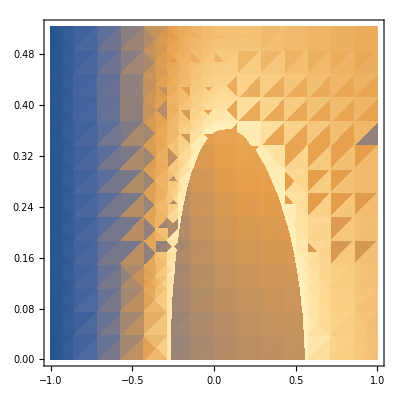

```mathematica
DensityPlot[FT[1,e,o],{e,-1,1},{o,0,π/6}]
```

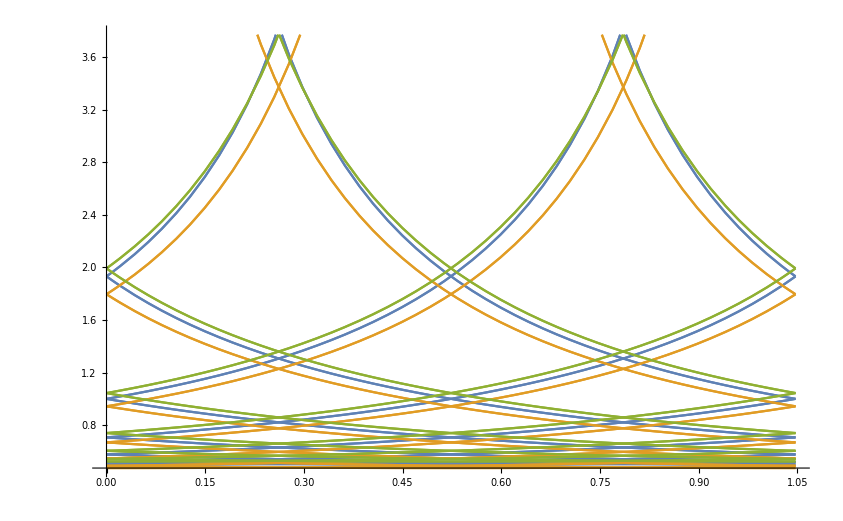

```mathematica
Plot[{FT[1,0,o],FT[1,-0.1,o],FT[1,0.1,o]},{o,0,π/3}]
```

```mathematica
Plot3D[FT[1,e,o],{e,-1,1},{o,0,2*π},PlotRange->{{-1,1},{0,2*π},{0,10}},PlotPoints->50]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

```mathematica
ContourPlot[FT[1,e,o],{e,-1,1},{o,0,2*π},PlotRange->{{-1,1},{0,2*π},{0,10}}]
```

-Graphics-